# Supplimentary Information

## To accompany: Intramolecular charge and energy transfer rates with reduced modes: comparison to Marcus theory for donor-bridge-acceptor systems

Xunmo Yang and Eric R Bittner

University of Houston

Department of Chemistry

## Initialization

### Load Core routines

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["PhysicalConstants`"];  (* this package is outdated...but highly useful! *)


(* place this file in the same directory as the Notebook or in the default load path of Mathematica *)
<< ModeAnalysis.m;
```

### conversion factors

```mathematica
hartree = 27.211396132 ElectronVolt(* eV *);
Bohr = 0.5291772108 Angstrom;
ℏ=hbar=PlanckConstantReduced;
```

### Read in files

```mathematica
name={"c13ea","c13ee","c14ea","c14ee","d26ae","d26ea","d26ee","d27ae","d27ea","d27ee","mmm"};
path="qchemout/"<>#<>".rtf"&/@name;
```

Read info from QChem output files and begin analysis.

```mathematica
kkk=4;  (* in this case we are looking at c14ee *)

RotMat=ReadRotM[path[[kkk]]];

Ene=ReadEne[path[[kkk]]];

{NAtom, dof, AtomicMass, AngFreq, RedMass, NormMode}=ReadNormalModes[path[[kkk]]];

Grads=ReadGradient[path[[kkk]],NAtom];


ω=FreqeV=Table[Convert[2Pi SpeedOfLight AngFreq[[i]]Centimeter^-1 PlanckConstantReduced,ElectronVolt]/ElectronVolt,{i,1,dof}];

Freq=Table[Convert[2Pi SpeedOfLight AngFreq[[i]]Centimeter^-1 ,Second^-1],{i,1,dof}];

NormModeInCartesian=Table[Table[NormMode[[m,i,j]]√AtomicMass[[i]]/√RedMass[[m]]//Simplify//Chop,{i,NAtom},{j,3}],{m,1,dof}];

Force=Table[Sum[NormModeInCartesian[[m]][[i,j]]*Grads[[i,j]]/√AtomicMass[[i]]//Simplify//Chop,{i,1,NAtom},{j,1,3}],{m,1,dof}];

GGG=CouplingConstant=Table[Convert[Force[[m]]hartree/Bohr√(PlanckConstantReduced/(2 Freq[[m]]AMU)),ElectronVolt]/.ElectronVolt->1//Simplify//Chop,{m,1,dof}];

G=G0=Table[({{RotMat[[1,2]]^2, RotMat[[2,2]]RotMat[[1,2]]}, {RotMat[[2,2]]RotMat[[1,2]], RotMat[[2,2]]^2}})*CouplingConstant[[m]]//Simplify//Chop,{m,1,dof}];
```

### Mode Analysis Routines

#### Analyze n projected modes

```mathematica
ModeAnalysis[n_]:=Module[{ωprime},
Clear[imax];
imax=n;
{ωprime,g}=NMode[n,hmat,M,Gnew];
Clear[ω,G];
ω=Take[ωprime,imax];

G=Table[({{RotMat[[1,2]]^2, RotMat[[2,2]]RotMat[[1,2]]}, {RotMat[[2,2]]RotMat[[1,2]], RotMat[[2,2]]^2}})*g[[m]]//Simplify//Chop,{m,1,imax}];


v12tab[kkk][imax]=Table[{t,V[1,2,t]},{t,0,nstep*tstep,tstep}];
v21tab[kkk][imax]=Table[{t,V[2,1,t]},{t,0,nstep*tstep,tstep}];

v12[kkk][imax]= Interpolation[v12tab[kkk][imax]];
v21[kkk][imax]= Interpolation[v21tab[kkk][imax]];
b12tab[kkk][imax]=Table[{t,Bd[1,2,t]},{t,0,nstep*tstep,tstep}];
b21tab[kkk][imax]=Table[{t,Bd[2,1,t]},{t,0,nstep*tstep,tstep}];
b12d[kkk][imax]= Interpolation[b12tab[kkk][imax]];
b21d[kkk][imax]= Interpolation[b21tab[kkk][imax]];
]
```

#### Analyze n random modes

```mathematica
RandomModeAnalysis[n_,freq_,FC_,seed_]:=Module[{g},
imax=n;
Clear[ω,G];
ω=Table[freq[[seed[[i]]]],{i,1,imax}];
g=Table[FC[[seed[[i]]]],{i,1,imax}];
G=Table[({{RotMat[[1,2]]^2, RotMat[[2,2]]RotMat[[1,2]]}, {RotMat[[2,2]]RotMat[[1,2]], RotMat[[2,2]]^2}})*g[[m]]//Simplify//Chop,{m,1,imax}];
Rv12tab[kkk][imax]=Table[{t,V[1,2,t]},{t,0,nstep*tstep,tstep}];Rv21tab[kkk][imax]=Table[{t,V[2,1,t]},{t,0,nstep*tstep,tstep}];
Rv12[kkk][imax]= Interpolation[Rv12tab[kkk][imax]];
Rv21[kkk][imax]= Interpolation[Rv21tab[kkk][imax]];
Rb12tab[kkk][imax]=Table[{t,Bd[1,2,t]},{t,0,nstep*tstep,tstep}];
Rb21tab[kkk][imax]=Table[{t,Bd[2,1,t]},{t,0,nstep*tstep,tstep}];
Rb12d[kkk][imax]= Interpolation[Rb12tab[kkk][imax]];
Rb21d[kkk][imax]= Interpolation[Rb21tab[kkk][imax]];
]
```

#### Analyze n strongest coupling modes

```mathematica
StrongestModeAnalysis[n_,freq_,FC_]:=Module[{g,tmp},
imax=n;
Clear[ω,G];
tmp=Transpose[Sort[Table[{freq[[i]],FC[[i]]},{i,1,dof}],Abs[#1[[2]]]>Abs[#2[[2]]]&]];
ω=Take[tmp[[1]],imax];
g=Take[tmp[[2]],imax];
G=Table[({{RotMat[[1,2]]^2, RotMat[[2,2]]RotMat[[1,2]]}, {RotMat[[2,2]]RotMat[[1,2]], RotMat[[2,2]]^2}})*g[[m]]//Simplify//Chop,{m,1,imax}];
Rv12tab[kkk][imax]=Table[{t,V[1,2,t]},{t,0,nstep*tstep,tstep}];
Sv21tab[kkk][imax]=Table[{t,V[2,1,t]},{t,0,nstep*tstep,tstep}];
Rv12[kkk][imax]= Interpolation[Rv12tab[kkk][imax]];
Sv21[kkk][imax]= Interpolation[Sv21tab[kkk][imax]];
Rb12tab[kkk][imax]=Table[{t,Bd[1,2,t]},{t,0,nstep*tstep,tstep}];
Sb21tab[kkk][imax]=Table[{t,Bd[2,1,t]},{t,0,nstep*tstep,tstep}];
Rb12d[kkk][imax]= Interpolation[Rb12tab[kkk][imax]];
Sb21d[kkk][imax]= Interpolation[Sb21tab[kkk][imax]];]
```

#### Calculation of Correlation Functions

```mathematica
nstep=3000;
tstep=0.14;
imin=1;
imax=dof;
Temperature = 298 Kelvin;

ℏ=hbar= 6.582122*10^(-4)(* eV/ps^-1 =Convert[PlanckConstantReduced /10^-12 /Second,ElectronVolt]*);
β=Convert[1/(Temperature BoltzmannConstant),ElectronVolt^-1]/.ElectronVolt->1;
Clear[ϵ];
ϵ[n_]:=Ene[[n]]-Sum[(G[[i,n,n]]^2/ω[[i]]),{i,imin,imax}];
nu[i_]:=1/(Exp[β*ω[[i]]]-1);

Δ[n_,m_,i_]:=(G[[i,n,n]]-G[[i,m,m]])/ω[[i]];
Ω[n_,m_,i_]:=(G[[i,n,n]]+G[[i,m,m]])/ω[[i]];

f[n_,m_,τ_]:=Exp[-2*Sum[(nu[i]+0.5)*(Δ[n,m,i])^2*(1-Cos[ω[[i]]*τ]),{i,imin,imax}]];

q[n_,m_,τ_]:=Exp[ⅈ*Sum[(Δ[n,m,i])^2*Sin[ω[[i]]*τ],{i,imin,imax}]];

o[n_,m_,τ_]:=(Sum[G[[i,n,m]]*(Δ[n,m,i]*
(nu[i]+1)Exp[ⅈ*ω[[i]]*τ]-Δ[n,m,i]*
nu[i]*Exp[-ⅈ*ω[[i]]*τ]+Ω[n,m,i]),{i,imin,imax}])^2+Sum[G[[i,n,m]]*G[[i,m,n]]*((nu[i]+1)Exp[ⅈ*ω[[i]]*τ]+nu[i]Exp[-ⅈ*ω[[i]]*τ]),{i,imin,imax}];
V[m_,n_,τ_]:=2*f[n,m,τ]*Re[Exp[-ⅈ*(ϵ[n]-ϵ[m])*τ]*q[n,m,τ]*o[n,m,τ]];
Bd[m_,n_,τ_]:=f[n,m,τ]*q[n,m,τ]*o[n,m,τ];
```

## Get G and ω

```mathematica
hess = FreqeV^2;
hmat = DiagonalMatrix[hess];
```

This  gives a fully sorted tridiagonal matrix. 
You may encouter singular matrix error for certain molecules, c14ee for example, because some couplings are zero. 
Manually abort it and continue.

```mathematica
Project1by1[{CouplingConstant},hmat];
```

Inverse::sing: Matrix {{0}} is singular.

Thread::tdlen: Objects of unequal length in {0}\ {{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 82 »}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 82 »}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 82 »}, « 46 », {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 82 »}, « 82 »} cannot be combined.

Thread::tdlen: Objects of unequal length in -{0}\ {{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 82 »}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 82 »}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 82 »}, « 46 », {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 82 »}, « 82 »} cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

$Aborted

```mathematica
ModeAnalysis[dof](*Exact calculation*)
```

```mathematica
ModeAnalysis[1](*Do however many mode you like.*)
ModeAnalysis[4]
ModeAnalysis[7]
```

```mathematica
Do[ModeAnalysis[i],{i,5,20,5}]
```

## Rate

```mathematica
φ12=Table[NIntegrate[v12[kkk][dof][τ],{τ,i*tstep,(i+1)*tstep}],{i,0,nstep-1}];
φ21=Table[NIntegrate[v21[kkk][dof][τ],{τ,i*tstep,(i+1)*tstep}],{i,0,nstep-1}];
Ww12={{0,0}};
Ww21={{0,0}};
ωω12=0;
ωω21=0;
Do[ωω12p=ωω12+φ12[[i]];
Ww12=Append[Ww12,{i*tstep*ℏ,ωω12p}];
ωω12=ωω12p,{i,nstep}];
Do[ωω21p=ωω21+φ21[[i]];
Ww21=Append[Ww21,{i*tstep*ℏ,ωω21p}];
ωω21=ωω21p,{i,nstep}];
W12t= Interpolation[Ww12];
W21t= Interpolation[Ww21];
vm12=Mean@Take[Table[Ww12[[i]][[2]],{i,1,nstep}],-30];
vm21=Mean@Take[Table[Ww21[[i]][[2]],{i,1,nstep}],-100];
W12=Function[Piecewise[{{W12t[#],0≤#≤nstep*tstep},{vm12 ,#>nstep*tstep*ℏ}}]];
W21=Function[Piecewise[{{W21t[#],0≤#≤nstep*tstep},{vm21 ,#>nstep*tstep*ℏ}}]];
Print["Golden rule rate =",vm21/ℏ*10^12,"s^-1"];
```

Golden rule rate =3.65596×10^9s^-1

## Correlation function

### Projected modes

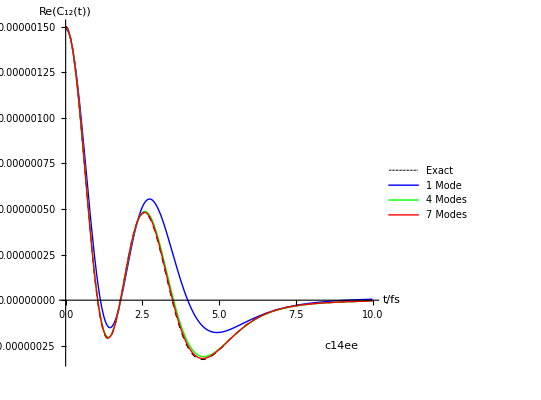

```mathematica
Plot[{
Re[b21d[kkk][dof][.001t/ℏ]],Re[b21d[kkk][1][.001t/ℏ]],Re[b21d[kkk][4][.001t/ℏ]],Re[b21d[kkk][7][.001t/ℏ]]},
{t,0,10},
PlotRange->All,
 AspectRatio->1,
PlotStyle->{{Black,Thick,Dashing[0.01]},Blue,Green,Red,Purple},
(*AxesOrigin-> {0,-0.4},*)
LabelStyle->16,
AxesLabel->{"t/fs","Re(C_12(t))"},
PlotLegends->Placed[{"Exact","1 Mode","4 Modes","7 Modes","7 Modes"},Right],
Epilog-> {Style[Text[name[[kkk]],{9,-2.5*10^-7}],24]}]
```

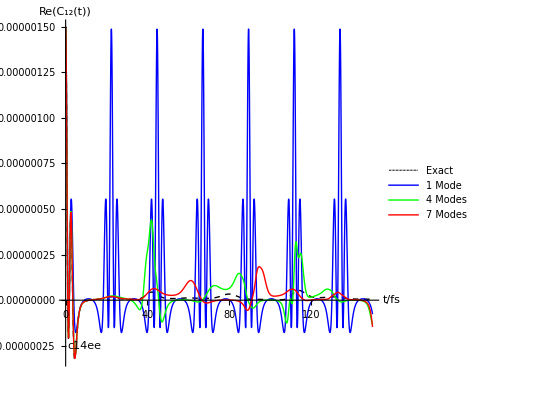

```mathematica
Plot[{
Re[b21d[kkk][dof][.001t/ℏ]],Re[b21d[kkk][1][.001t/ℏ]],Re[b21d[kkk][4][.001t/ℏ]],Re[b21d[kkk][7][.001t/ℏ]]},
{t,0,150},
PlotRange->All,
 AspectRatio->1,
PlotStyle->{{Black,Thick,Dashing[0.01]},Blue,Green,Red,Purple},
(*AxesOrigin-> {0,-0.4},*)
LabelStyle->16,
AxesLabel->{"t/fs","Re(C_12(t))"},
PlotLegends->Placed[{"Exact","1 Mode","4 Modes","7 Modes","7 Modes"},Right],
Epilog-> {Style[Text[name[[kkk]],{9,-2.5*10^-7}],24]}]
```

### Random modes

```mathematica
seed=RandomSample[Range[dof]];
```

```mathematica
RandomModeAnalysis[70,FreqeV,GGG,seed]
RandomModeAnalysis[110,FreqeV,GGG,seed]
RandomModeAnalysis[130,FreqeV,GGG,seed]
```

```mathematica
RandomModeAnalysis[110,FreqeV,GGG,seed]
```

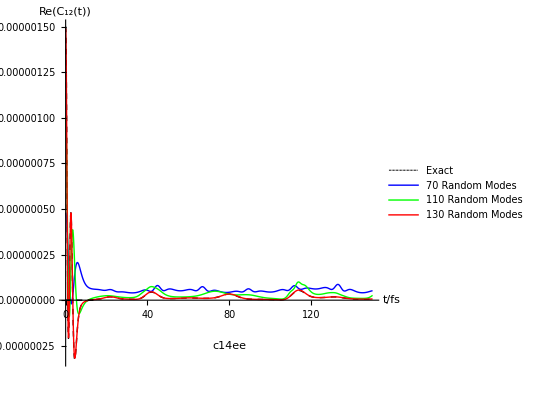

```mathematica
Plot[{
Re[b21d[kkk][dof][.001t/ℏ]],Re[Rb21d[kkk][70][0.001t/ℏ]],Re[Rb21d[kkk][110][0.001t/ℏ]],Re[Rb21d[kkk][130][0.001t/ℏ]]},
{t,0,150},
PlotRange->All,
 AspectRatio->1,
PlotStyle->{{Black,Thick,Dashing[0.01]},Blue,Green,Red,Purple},
(*AxesOrigin-> {0,-0.4},*)
LabelStyle->16,
AxesLabel->{"t/fs","Re(C_12(t))"},
PlotLegends->Placed[{"Exact","70 Random Modes","110 Random Modes","130 Random Modes"},Right],
Epilog-> {Style[Text["c14ee",{80,-2.5*10^-7}],24],{Dashing[0.01],Line[{{0,0},{15,0}}]},
Inset[Plot[{
Re[b21d[kkk][dof][.001t/ℏ]],Re[Rb21d[kkk][70][0.001t/ℏ]],Re[Rb21d[kkk][110][0.001t/ℏ]],Re[Rb21d[kkk][130][0.001t/ℏ]]},
{t,0,20},Frame->True,FrameTicks->{True,False},PlotRange->All,(*FrameLabel->{"t/fs","Re(C_12(t))"}*)ImageSize->200,PlotStyle->{{Black,Thick,Dashing[0.01]},Blue,Green,Red,Purple}],{90,8*10^-7}]}]
```

### Strongest Couplings

```mathematica
Do[StrongestModeAnalysis[i,FreqeV,GGG],{i,10,50,20}]
```

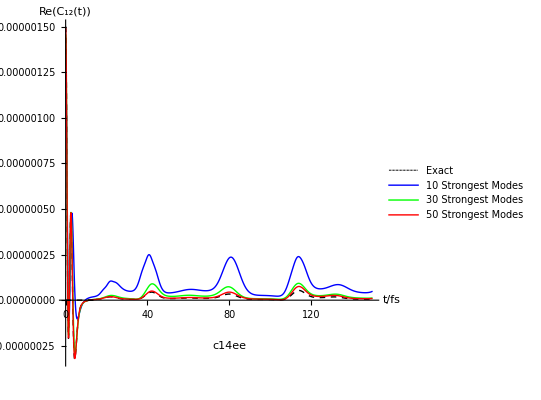

```mathematica
Plot[{
Re[b21d[kkk][dof][.001t/ℏ]],Re[Sb21d[kkk][10][0.001t/ℏ]],Re[Sb21d[kkk][30][0.001t/ℏ]],Re[Sb21d[kkk][50][0.001t/ℏ]]},
{t,0,150},
PlotRange->All,
 AspectRatio->1,
PlotStyle->{{Black,Thick,Dashing[0.01]},Blue,Green,Red,Purple},
(*AxesOrigin-> {0,-0.4},*)
LabelStyle->16,
AxesLabel->{"t/fs","Re(C_12(t))"},
PlotLegends->Placed[{"Exact","10 Strongest Modes","30 Strongest Modes","50 Strongest Modes","70 Strongest Modes","110 Strongest Modes","130 Strongest Modes","90 Strongest Modes","110 Strongest Modes"},Right],
Epilog-> {Style[Text["c14ee",{80,-2.5*10^-7}],24],{Dashing[0.01],Line[{{0,0},{15,0}}]},
Inset[Plot[{
Re[b21d[kkk][dof][.001t/ℏ]],Re[Sb21d[kkk][10][0.001t/ℏ]],Re[Sb21d[kkk][30][0.001t/ℏ]],Re[Sb21d[kkk][50][0.001t/ℏ]]},
{t,0,7},Frame->True,FrameTicks->{True,False},PlotRange->All,PlotStyle->{{Black,Thick,Dashing[0.01]},Blue,Green,Red,Purple},(*FrameLabel->{"t/fs","Re(C_12(t))"}*)ImageSize->220],{80,9*10^-7}]}]
```

### Comparison

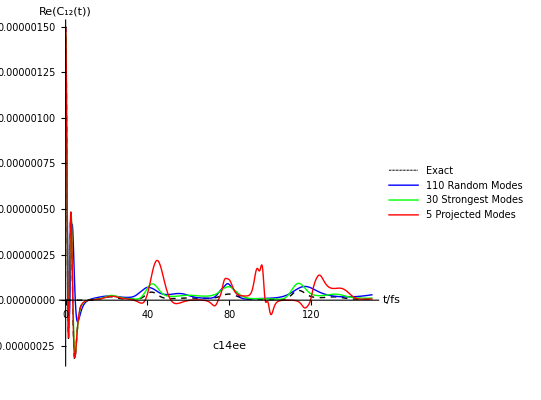

```mathematica
Plot[{
Re[b21d[kkk][dof][.001t/ℏ]],Re[Rb21d[kkk][110][0.001t/ℏ]],Re[Sb21d[kkk][30][0.001t/ℏ]],Re[b21d[kkk][5][0.001t/ℏ]]},
{t,0,150},
PlotRange->All,
 AspectRatio->1,
PlotStyle->{{Black,Thick,Dashing[0.01]},Blue,Green,Red,Purple},
(*AxesOrigin-> {0,-0.4},*)
LabelStyle->16,
AxesLabel->{"t/fs","Re(C_12(t))"},
PlotLegends->Placed[{"Exact","110 Random Modes","30 Strongest Modes","5 Projected Modes","150 Random Modes","90 Random Modes","110 Random Modes"},Right],
Epilog-> {Style[Text["c14ee",{80,-2.5*10^-7}],24],{Dashing[0.01],Line[{{0,0},{15,0}}]},
Inset[Plot[{
Re[b21d[kkk][dof][.001t/ℏ]],Re[Rb21d[kkk][110][0.001t/ℏ]],Re[Sb21d[kkk][30][0.001t/ℏ]],Re[b21d[kkk][5][0.001t/ℏ]]},
{t,0,7},Frame->True,FrameTicks->{True,False},PlotRange->All,PlotStyle->{{Black,Thick,Dashing[0.01]},Blue,Green,Red,Purple},(*FrameLabel->{"t/fs","Re(C_12(t))"}*)ImageSize->220],{80,9*10^-7}]}]
```